## Functions and Rules

## Syntax Reminders

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

For numerical expressions:  exact input ⟹ exact output,  approx input ⟹ approx output

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

### Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively one can use a Palette such as the Basic Math Assistant.

### Replacement Rules

See Transformation Rules and Definitions.

Solutions to equations are returned as a list of lists of replacement rules.

```mathematica
sol=Solve[{a x^2+b y==0,c x+d y==0},{x,y}]
```

{{y→0,x→0},{y→-(b c^2)/(a d^2),x→(b c)/(a d)}}

To use the solutions, the ReplaceAll (/.) command is used. Here we substitute both solutions into both equations.

```mathematica
{a x^2+b y==0,c x+d y==0}/.sol
```

(True | True
True | True)

Substitute the second solution into the variable x.

```mathematica
x/.sol⟦2⟧
```

(b c)/(a d)

Remove this definition.

```mathematica
Remove[sol]
```

### Defining Functions

See Making Definitions for Functions.

Define the function, f(x)=x^2+1.

```mathematica
f[x_]:=x^2+1
```

Note that the symbol f went from blue = undefined to black = defined.

Here is f(2)

```mathematica
f[2]
```

5

To see what definitions are associated with a symbol, use ?

```mathematica
?f
```

Global`f

f[x_]:=x^2+1

Clear this definition.

```mathematica
Clear[f]
```

The symbol f has now returned to being blue.

```mathematica
?f
```

Global`f

### Defining Vector Functions

Define g(x,y)=(y,x+y), a vector function (or map) g:ℝ^2→ℝ^2.

```mathematica
g[{x_,y_}]:={y,x+y}
```

Compute g(a,b).

```mathematica
g[{a,b}]
```

{b,a+b}

Note that g takes a vector and returns a vector. This is useful when composing (nesting or iterating) vector functions.

Compute g∘g(x,y).

```mathematica
g[{x,y}]
```

{y,x+y}

```mathematica
g[%]
```

{x+y,x+2 y}

Remove this definition.

```mathematica
Clear[g]
```

## Function Definitions

Define the function y(x)=x ⅇ^(-x/10)sin(x). Plot y(x) over 0≤x≤10π. Compute and simplify c_n=∫_0^(n π) y(x)ⅆx for n∈ℤ.  Use DiscretePlot to visualize c_n for integer n=1,2,…,20.  [4 Marks]

Solution

Define the function y(x)=x ⅇ^(-x/10)sin(x). [1 Mark]

```mathematica
y[x_]:=x ⅇ^(-x/10) Sin[x]
```

Plot y(x) over 0≤x≤10π. [1 Mark]

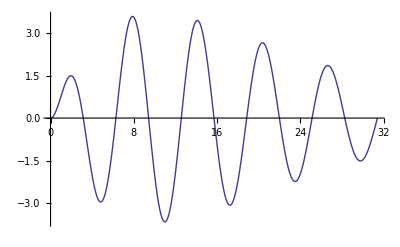

```mathematica
Plot[y[x],{x,0,10 π}]
```

Compute and simplify c_n=∫_0^(n π) y(x)ⅆx for n∈ℤ. [1 Mark]

```mathematica
∫_0^(n π) f[x]ⅆx
```

(10 (ⅇ^(-(π n)/10) ((990-101 π n) sin(π n)-10 (101 π n+20) cos(π n))+200))/10201

```mathematica
Subscript[c, n_]=Simplify[%,n∈ℤ]
```

-(100 ⅇ^(-(π n)/10) ((-1)^n (101 π n+20)-20 ⅇ^((π n)/10)))/10201

Use DiscretePlot to visualize c_n for integer n=1,2,…,20. [1 Mark]

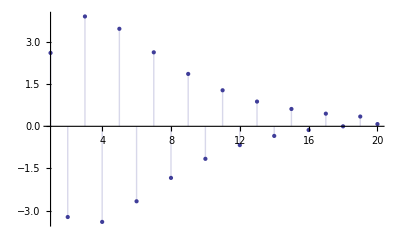

```mathematica
DiscretePlot[Subscript[c, n],{n,1,20}]
```

Define the vector function h(x,y)=((x+y)/2,√(x y)), a vector function (or map) h:ℝ^2→ℝ^2. Iterate this function 4 times for five different random starting vectors {x,y} with x,y>0. You can use NestList or FixedPointList to perform this iteration. What do you observe about the final vector in each case? [3 Marks]

Solution

Define the vector function h(x,y)=((x+y)/2,√(x y)). [1 Mark]

```mathematica
h[{x_,y_}]:={(x+y)/2,√(x y)}
```

Iterate this function 4 times for five different random starting vectors {x,y} with x,y>0. [1 Mark]

```mathematica
randvect:=RandomReal[{0,10},{2}]
```

```mathematica
h[h[h[h[randvect]]]]
```

{1.1539,1.15389}

You can use NestList to perform this iteration:

```mathematica
Table[NestList[h,randvect,4],{5}]
```

({8.56453,1.15291} | {4.85872,3.14231} | {4.00051,3.90738} | {3.95395,3.95367} | {3.95381,3.95381}
{6.87755,5.24794} | {6.06274,6.00774} | {6.03524,6.03518} | {6.03521,6.03521} | {6.03521,6.03521}
{0.163905,9.14988} | {4.65689,1.22463} | {2.94076,2.38809} | {2.66442,2.65005} | {2.65724,2.65723}
{3.6269,0.402809} | {2.01485,1.2087} | {1.61177,1.56056} | {1.58617,1.58596} | {1.58606,1.58606}
{5.90115,6.02448} | {5.96282,5.9625} | {5.96266,5.96266} | {5.96266,5.96266} | {5.96266,5.96266})

Or use FixedPointList:

```mathematica
Table[FixedPointList[h,randvect],{5}]
```

{(6.42965 | 9.50703
7.96834 | 7.81837
7.89336 | 7.893
7.89318 | 7.89318
7.89318 | 7.89318
7.89318 | 7.89318),(2.84626 | 2.42622
2.63624 | 2.62786
2.63205 | 2.63204
2.63205 | 2.63205
2.63205 | 2.63205
2.63205 | 2.63205),(9.94272 | 4.69103
7.31688 | 6.82947
7.07317 | 7.06897
7.07107 | 7.07107
7.07107 | 7.07107
7.07107 | 7.07107
7.07107 | 7.07107),(1.4906 | 2.35673
1.92367 | 1.87429
1.89898 | 1.89882
1.8989 | 1.8989
1.8989 | 1.8989
1.8989 | 1.8989),(0.615045 | 2.26786
1.44145 | 1.18103
1.31124 | 1.30476
1.308 | 1.308
1.308 | 1.308
1.308 | 1.308
1.308 | 1.308)}

It is clear that these two sequences for x_n and y_n converge to the same number, which is the arithmetic-geometric mean (AGM) of x and y.

## Replacement Rules and Condition

Use Range to construct a list of the first 2000 integers. Write a replacement rule using Condition (/;) to replace all prime numbers in this list by 0. What is the Total of the resulting list? [3 Marks]

Solution

Use Range to construct a list of the first 2000 integers. [1 Mark]

```mathematica
Range[2000];
```

Write a replacement rule using Condition (/;) to replace all prime numbers in this list by 0. [1 Mark]

```mathematica
%/.x_/;PrimeQ[x]->0
```

{1,0,0,4,0,6,0,8,9,10,0,12,0,14,15,16,0,18,0,20,21,22,0,24,25,26,27,28,0,30,0,32,33,34,35,36,0,38,39,40,0,42,0,44,45,46,0,48,49,50,51,52,0,54,55,56,57,58,0,60,0,62,63,64,65,66,0,68,69,70,0,72,0,74,75,76,77,78,0,80,81,82,0,84,85,86,87,88,0,90,91,92,93,94,95,96,0,98,99,100,0,102,0,104,105,106,0,108,0,110,111,112,0,114,115,116,117,118,119,120,121,122,123,124,125,126,0,128,129,130,0,132,133,134,135,136,0,138,0,140,141,142,143,144,145,146,147,148,0,150,0,152,153,154,155,156,0,158,159,160,161,162,0,164,165,166,0,168,169,170,171,172,0,174,175,176,177,178,0,180,0,182,183,184,185,186,187,188,189,190,0,192,0,194,195,196,0,198,0,200,201,202,203,204,205,206,207,208,209,210,0,212,213,214,215,216,217,218,219,220,221,222,0,224,225,226,0,228,0,230,231,232,0,234,235,236,237,238,0,240,0,242,243,244,245,246,247,248,249,250,0,252,253,254,255,256,0,258,259,260,261,262,0,264,265,266,267,268,0,270,0,272,273,274,275,276,0,278,279,280,0,282,0,284,285,286,287,288,289,290,291,292,0,294,295,296,297,298,299,300,301,302,303,304,305,306,0,308,309,310,0,312,0,314,315,316,0,318,319,320,321,322,323,324,325,326,327,328,329,330,0,332,333,334,335,336,0,338,339,340,341,342,343,344,345,346,0,348,0,350,351,352,0,354,355,356,357,358,0,360,361,362,363,364,365,366,0,368,369,370,371,372,0,374,375,376,377,378,0,380,381,382,0,384,385,386,387,388,0,390,391,392,393,394,395,396,0,398,399,400,0,402,403,404,405,406,407,408,0,410,411,412,413,414,415,416,417,418,0,420,0,422,423,424,425,426,427,428,429,430,0,432,0,434,435,436,437,438,0,440,441,442,0,444,445,446,447,448,0,450,451,452,453,454,455,456,0,458,459,460,0,462,0,464,465,466,0,468,469,470,471,472,473,474,475,476,477,478,0,480,481,482,483,484,485,486,0,488,489,490,0,492,493,494,495,496,497,498,0,500,501,502,0,504,505,506,507,508,0,510,511,512,513,514,515,516,517,518,519,520,0,522,0,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,0,542,543,544,545,546,0,548,549,550,551,552,553,554,555,556,0,558,559,560,561,562,0,564,565,566,567,568,0,570,0,572,573,574,575,576,0,578,579,580,581,582,583,584,585,586,0,588,589,590,591,592,0,594,595,596,597,598,0,600,0,602,603,604,605,606,0,608,609,610,611,612,0,614,615,616,0,618,0,620,621,622,623,624,625,626,627,628,629,630,0,632,633,634,635,636,637,638,639,640,0,642,0,644,645,646,0,648,649,650,651,652,0,654,655,656,657,658,0,660,0,662,663,664,665,666,667,668,669,670,671,672,0,674,675,676,0,678,679,680,681,682,0,684,685,686,687,688,689,690,0,692,693,694,695,696,697,698,699,700,0,702,703,704,705,706,707,708,0,710,711,712,713,714,715,716,717,718,0,720,721,722,723,724,725,726,0,728,729,730,731,732,0,734,735,736,737,738,0,740,741,742,0,744,745,746,747,748,749,750,0,752,753,754,755,756,0,758,759,760,0,762,763,764,765,766,767,768,0,770,771,772,0,774,775,776,777,778,779,780,781,782,783,784,785,786,0,788,789,790,791,792,793,794,795,796,0,798,799,800,801,802,803,804,805,806,807,808,0,810,0,812,813,814,815,816,817,818,819,820,0,822,0,824,825,826,0,828,0,830,831,832,833,834,835,836,837,838,0,840,841,842,843,844,845,846,847,848,849,850,851,852,0,854,855,856,0,858,0,860,861,862,0,864,865,866,867,868,869,870,871,872,873,874,875,876,0,878,879,880,0,882,0,884,885,886,0,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,0,908,909,910,0,912,913,914,915,916,917,918,0,920,921,922,923,924,925,926,927,928,0,930,931,932,933,934,935,936,0,938,939,940,0,942,943,944,945,946,0,948,949,950,951,952,0,954,955,956,957,958,959,960,961,962,963,964,965,966,0,968,969,970,0,972,973,974,975,976,0,978,979,980,981,982,0,984,985,986,987,988,989,990,0,992,993,994,995,996,0,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,0,1010,1011,1012,0,1014,1015,1016,1017,1018,0,1020,0,1022,1023,1024,1025,1026,1027,1028,1029,1030,0,1032,0,1034,1035,1036,1037,1038,0,1040,1041,1042,1043,1044,1045,1046,1047,1048,0,1050,0,1052,1053,1054,1055,1056,1057,1058,1059,1060,0,1062,0,1064,1065,1066,1067,1068,0,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,0,1088,1089,1090,0,1092,0,1094,1095,1096,0,1098,1099,1100,1101,1102,0,1104,1105,1106,1107,1108,0,1110,1111,1112,1113,1114,1115,1116,0,1118,1119,1120,1121,1122,0,1124,1125,1126,1127,1128,0,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,0,1152,0,1154,1155,1156,1157,1158,1159,1160,1161,1162,0,1164,1165,1166,1167,1168,1169,1170,0,1172,1173,1174,1175,1176,1177,1178,1179,1180,0,1182,1183,1184,1185,1186,0,1188,1189,1190,1191,1192,0,1194,1195,1196,1197,1198,1199,1200,0,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,0,1214,1215,1216,0,1218,1219,1220,1221,1222,0,1224,1225,1226,1227,1228,0,1230,0,1232,1233,1234,1235,1236,0,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,0,1250,1251,1252,1253,1254,1255,1256,1257,1258,0,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,0,1278,0,1280,1281,1282,0,1284,1285,1286,1287,1288,0,1290,0,1292,1293,1294,1295,1296,0,1298,1299,1300,0,1302,0,1304,1305,1306,0,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,0,1320,0,1322,1323,1324,1325,1326,0,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,0,1362,1363,1364,1365,1366,0,1368,1369,1370,1371,1372,0,1374,1375,1376,1377,1378,1379,1380,0,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,0,1400,1401,1402,1403,1404,1405,1406,1407,1408,0,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,0,1424,1425,1426,0,1428,0,1430,1431,1432,0,1434,1435,1436,1437,1438,0,1440,1441,1442,1443,1444,1445,1446,0,1448,1449,1450,0,1452,0,1454,1455,1456,1457,1458,0,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,0,1472,1473,1474,1475,1476,1477,1478,1479,1480,0,1482,0,1484,1485,1486,0,1488,0,1490,1491,1492,0,1494,1495,1496,1497,1498,0,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,0,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,0,1524,1525,1526,1527,1528,1529,1530,0,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,0,1544,1545,1546,1547,1548,0,1550,1551,1552,0,1554,1555,1556,1557,1558,0,1560,1561,1562,1563,1564,1565,1566,0,1568,1569,1570,0,1572,1573,1574,1575,1576,1577,1578,0,1580,1581,1582,0,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,0,1598,1599,1600,0,1602,1603,1604,1605,1606,0,1608,0,1610,1611,1612,0,1614,1615,1616,1617,1618,0,1620,0,1622,1623,1624,1625,1626,0,1628,1629,1630,1631,1632,1633,1634,1635,1636,0,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,0,1658,1659,1660,1661,1662,0,1664,1665,1666,0,1668,0,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,0,1694,1695,1696,0,1698,0,1700,1701,1702,1703,1704,1705,1706,1707,1708,0,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,0,1722,0,1724,1725,1726,1727,1728,1729,1730,1731,1732,0,1734,1735,1736,1737,1738,1739,1740,0,1742,1743,1744,1745,1746,0,1748,1749,1750,1751,1752,0,1754,1755,1756,1757,1758,0,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,0,1778,1779,1780,1781,1782,0,1784,1785,1786,0,1788,0,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,0,1802,1803,1804,1805,1806,1807,1808,1809,1810,0,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,0,1824,1825,1826,1827,1828,1829,1830,0,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,0,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,0,1862,1863,1864,1865,1866,0,1868,1869,1870,0,1872,0,1874,1875,1876,0,1878,0,1880,1881,1882,1883,1884,1885,1886,1887,1888,0,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,0,1902,1903,1904,1905,1906,0,1908,1909,1910,1911,1912,0,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,0,1932,0,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,0,1950,0,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,0,1974,1975,1976,1977,1978,0,1980,1981,1982,1983,1984,1985,1986,0,1988,1989,1990,1991,1992,0,1994,1995,1996,0,1998,0,2000}

Compute the Total of the resulting list. [1 Mark]

```mathematica
Total[%]
```

1723950

## Rule-based Programming

Consider the numbers p_n defined by p_n=1/(n+2) p_(n-1)+(n-1)/(n+2)p_(n-2) with p_1=p_2=1.

Compute p_1, p_2,…,p_20 using rule-based programming. [2 Marks]

Use DiscretePlot to display log(n p_n) for 1≤n≤300 (NB: modify the rule-based code you wrote in the previous part so as to use dynamic programming, i.e., saving intermediate results). [2 Marks]

What happens to log(n p_n) for large n? What does this tell you about p_n for large n? [2 Marks]

Solution

Compute p_1, p_2,…,p_20 using rule-based programming. [2 Marks]

```mathematica
Subscript[p, 1]=1;Subscript[p, 2]=1;
```

```mathematica
Subscript[p, n_]:=1/(n+2) Subscript[p, n-1]+(n-1)/(n+2)Subscript[p, n-2]
```

```mathematica
Table[Subscript[p, n],{n,20}]
```

{1,1,3/5,3/5,3/7,3/7,1/3,1/3,3/11,3/11,3/13,3/13,1/5,1/5,3/17,3/17,3/19,3/19,1/7,1/7}

Use DiscretePlot and dynamic programmingto display log(n p_n) for 1≤n≤300. [2 Marks]

```mathematica
Subscript[p, n_]:=Subscript[p, n]=1/(n+2) Subscript[p, n-1]+(n-1)/(n+2)Subscript[p, n-2]
```

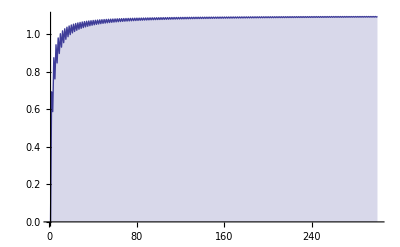

```mathematica
DiscretePlot[log(n Subscript[p, n]),{n,300}]
```

What happens to log(n p_n) for large n? What does this tell you about p_n for large n? [2 Marks]

The values tend to a constant. Since log(n p_n)→c we have p_n→ⅇ^c/n.

For this recurrence we can find the exact solution:

```mathematica
RSolve[{(n+2) p(n)==(n-1) p(n-2)+p(n-1),p(1)==1,p(2)==1},p(n),n]
```

{{p(n)→(3 (2 n+(-1)^n+3))/(2 (n+1) (n+2))}}

And determine the lim_(n→∞) n p_n

```mathematica
lim_(n->∞) n(3 (2 n+(-1)^n+3))/(2 (n+1) (n+2))
```

3

so p_n→3/n.

Write a rule-based program for a function der[f_,x] to compute the derivatives with respect to x of polyomials f. Verify that your program gives the correct answer for the derivative of a x^4+b x^2+c x+d with respect to x. [6 Marks]

Hint: For n an integer, f(x) and g(x) arbitrary polynomials in x, and c an arbitrary constant independent of x (lookup FreeQ and use a Condition), you will need to implement all the following rules:

(∂(f(x)+g(x)))/(∂x)==(∂f(x))/(∂x)+(∂g(x))/(∂x)
(∂(c f(x)))/(∂x)==c(∂(f(x)))/(∂x)
(∂c)/(∂x)==0
(∂x^n)/(∂x)==n x^(n-1)
(∂x)/(∂x)==1

Hint: The third rule can be implemented as

```mathematica
der[c_,x]:=0/;FreeQ[c,x]
```

Solution

Implement each of the rules. One can (and should) test out the application of the rules one at a time.

(∂(f(x)+g(x)))/(∂x)==(∂f(x))/(∂x)+(∂g(x))/(∂x) [1 Mark]

```mathematica
der[f_+g_,x]:=der[f,x]+der[g,x]
```

Test:

```mathematica
der[f[x]+g[x],x]
```

der(f(x),x)+der(g(x),x)

(∂(c f(x)))/(∂x)==c(∂(f(x)))/(∂x) for c independent of x [1 Mark]

```mathematica
der[c_ f_,x]:=c der[f,x]/;FreeQ[c,x]
```

Test:

```mathematica
der[a g[x],x]
```

a der(g(x),x)

(∂c)/(∂x)==0 for c independent of x [1 Mark]

```mathematica
der[c_,x]:=0/;FreeQ[c,x]
```

Test:

```mathematica
der[a,x]
```

0

(∂x^n)/(∂x)==n x^(n-1) for n independent of x [1 Mark]

```mathematica
der[x^n_,x]:=n x^(n-1)/;FreeQ[n,x]
```

Test:

```mathematica
der[x^3,x]
```

3 x^2

```mathematica
der[x^m,x]
```

m x^(m-1)

(∂x)/(∂x)==1 [1 Mark]

```mathematica
der[x,x]:=1
```

Verify that your program gives the correct answer for the derivative of a x^4+b x^2+c x+d with respect to x. [1 Mark]

```mathematica
der[a x^4+b x^2+c x+d,x]
```

4 a x^3+2 b x+c